# Gate fidelities for the depolarsing noise model

#### Pauli matrices

```mathematica
Id = IdentityMatrix[2];
pauliX=PauliMatrix[1];
pauliY=PauliMatrix[2];
pauliZ=PauliMatrix[3];
```

#### Physical basis elements

```mathematica
k0={{1,0}};
k1={{0,1}};
physicalplus=(k0+k1)/√2;
physicalminus=(k0-k1)/√2;
physicaliplus=(k0+ⅈ k1)/√2;
physicaliminus=(k0-ⅈ k1)/√2;
```

```mathematica
PhysicalCardinalStates=Table[ConjugateTranspose[q].q,{q,{k0,k1,physicalplus,physicalminus,physicaliplus,physicaliminus}}];
```

#### Logical basis elements

```mathematica
logical0=1/(√2)(KroneckerProduct[k0,k0,k0,k0]+KroneckerProduct[k1,k1,k1,k1]);
logical1=1/(√2)(KroneckerProduct[k0,k1,k0,k1]+KroneckerProduct[k1,k0,k1,k0]);
logicalplus=(logical0+logical1)/√2;
logicalminus=(logical0-logical1)/√2;
logicaliplus=(logical0+ⅈ logical1)/√2;
logicaliminus=(logical0-ⅈ logical1)/√2;
```

```mathematica
LogicalCardinalStates=Table[ConjugateTranspose[q].q,{q,{logical0,logical1,logicalplus,logicalminus,logicaliplus,logicaliminus}}];
```

### Logical Pauli Matrices in the code space

```mathematica
LId=ConjugateTranspose[logical0].logical0+ConjugateTranspose[logical1].logical1;
LPauliX=ConjugateTranspose[logical0].logical1+ConjugateTranspose[logical1].logical0;
LPauliY=-ⅈ ConjugateTranspose[logical0].logical1+ⅈ ConjugateTranspose[logical1].logical0;
LPauliZ=ConjugateTranspose[logical0].logical0-ConjugateTranspose[logical1].logical1;
```

### Stabilizer Projectors for the + 1 Codespace

```mathematica
Z1Z3=(IdentityMatrix[16]+KroneckerProduct[pauliZ,Id,pauliZ,Id])/2;
Z2Z4=(IdentityMatrix[16]+KroneckerProduct[Id,pauliZ,Id,pauliZ])/2;
X1X2X3X4=(IdentityMatrix[16]+KroneckerProduct[pauliX,pauliX,pauliX,pauliX])/2;
```

### Define the single qubit rotation gates

```mathematica
Rx[θ_]:=MatrixExp[-ⅈ θ/2 PauliMatrix[1]];
Ry[θ_]:=MatrixExp[-ⅈ θ/2 PauliMatrix[2]];
Rz[θ_]:=MatrixExp[-ⅈ θ/2 PauliMatrix[3]];
Rnθ[{nx_,ny_,nz_},θ_]:=MatrixExp[-ⅈ θ/2(nx PauliMatrix[1]+ny PauliMatrix[2]+nz PauliMatrix[3])];
```

### Define the logical operations for two node setup

```mathematica
RXπL=KroneckerProduct[Rx[π],Id,Rx[π],Id];
RzπL=KroneckerProduct[Rx[π],Rx[π],Ry[π],Ry[π]];
```

### Define the depolarising channel

```mathematica
Depolar[p_,ρ_]:=(1-p)ρ+p/3(Sum[PauliMatrix[i].ρ.ConjugateTranspose[PauliMatrix[i]],{i,1,3}]);
DepolarMultiQubit1[p_,ρ_]:=(1-p)ρ+p/3(Sum[KroneckerProduct[PauliMatrix[i],Id,Id,Id].ρ.KroneckerProduct[ConjugateTranspose[PauliMatrix[i]],Id,Id,Id],{i,1,3}]);
DepolarMultiQubit2[p_,ρ_]:=(1-p)ρ+p/3(Sum[KroneckerProduct[Id,PauliMatrix[i],Id,Id].ρ.KroneckerProduct[Id,ConjugateTranspose[PauliMatrix[i]],Id,Id],{i,1,3}]);
DepolarMultiQubit3[p_,ρ_]:=(1-p)ρ+p/3(Sum[KroneckerProduct[Id,Id,PauliMatrix[i],Id].ρ.KroneckerProduct[Id,Id,ConjugateTranspose[PauliMatrix[i]],Id],{i,1,3}]);
DepolarMultiQubit4[p_,ρ_]:=(1-p)ρ+p/3(Sum[KroneckerProduct[Id,Id,Id,PauliMatrix[i]].ρ.KroneckerProduct[Id,Id,Id,ConjugateTranspose[PauliMatrix[i]]],{i,1,3}]);
```

### Define fidelity via PTM

```mathematica
Fidelity[Rideal_,Rnoisy_]:=(Tr[ConjugateTranspose[Rideal].Rnoisy]+2)/6;
```

## Calculating the physical Pauli Transfer Matrix (PTM) and Gate Fidelity

```mathematica
CalculatePhysicalGateFidelity[DepolarRate_,Operation_]:=(NoisyPTM=IdentityMatrix[4];
												NoiselessPTM=IdentityMatrix[4];
												RoutNoisy=Range[6];
												RoutNoiseless=Range[6];
												For[i=1,i<=6,i++,
													inputstate=PhysicalCardinalStates[[i]];
													NoiselessOutput=Operation.inputstate.ConjugateTranspose[Operation]/Tr[Operation.inputstate.ConjugateTranspose[Operation]];
													NoisyOutput=Depolar[DepolarRate,Operation.inputstate.ConjugateTranspose[Operation]]/Tr[Depolar[DepolarRate,Operation.inputstate.ConjugateTranspose[Operation]]];
RoutNoisy[[i]]=Table[Tr[NoisyOutput.pauli],{pauli,{PauliMatrix[1],PauliMatrix[2],PauliMatrix[3]}}];															RoutNoiseless[[i]]=Table[Tr[NoiselessOutput.pauli],{pauli,{PauliMatrix[1],PauliMatrix[2],PauliMatrix[3]}}];
													];
												NoisyPTM[[1,1]]=1;
												NoisyPTM[[1,2]]=NoisyPTM[[1,3]]=NoisyPTM[[1,4]]=0;
												NoisyPTM[[2,2]]=0.5 (RoutNoisy[[3]][[1]]-RoutNoisy[[4]][[1]]);
												NoisyPTM[[3,3]]=0.5 (RoutNoisy[[5]][[2]]-RoutNoisy[[6]][[2]]);
												NoisyPTM[[4,4]]=0.5 (RoutNoisy[[1]][[3]]-RoutNoisy[[2]][[3]]);
												NoisyPTM[[2,1]]=0.5 (RoutNoisy[[1]][[1]]+RoutNoisy[[2]][[1]]);
												NoisyPTM[[3,1]]=0.5 (RoutNoisy[[1]][[2]]+RoutNoisy[[2]][[2]]);
												NoisyPTM[[4,1]]=0.5 (RoutNoisy[[1]][[3]]+RoutNoisy[[2]][[3]]);
												NoisyPTM[[3,2]]=0.5 (RoutNoisy[[3]][[2]]-RoutNoisy[[4]][[2]]);
												NoisyPTM[[4,2]]=0.5 (RoutNoisy[[3]][[3]]-RoutNoisy[[4]][[3]]);
												NoisyPTM[[2,3]]=0.5 (RoutNoisy[[5]][[1]]-RoutNoisy[[6]][[1]]);
												NoisyPTM[[4,3]]=0.5 (RoutNoisy[[5]][[3]]-RoutNoisy[[6]][[3]]);
												NoisyPTM[[2,4]]=0.5 (RoutNoisy[[1]][[1]]-RoutNoisy[[2]][[1]]);
												NoisyPTM[[3,4]]=0.5 (RoutNoisy[[1]][[2]]-RoutNoisy[[2]][[2]]);

												NoiselessPTM[[1,1]]=1;
												NoiselessPTM[[1,2]]=NoiselessPTM[[1,3]]=NoiselessPTM[[1,4]]=0;
												NoiselessPTM[[2,2]]=0.5 (RoutNoiseless[[3]][[1]]-RoutNoiseless[[4]][[1]]);
												NoiselessPTM[[3,3]]=0.5 (RoutNoiseless[[5]][[2]]-RoutNoiseless[[6]][[2]]);
												NoiselessPTM[[4,4]]=0.5 (RoutNoiseless[[1]][[3]]-RoutNoiseless[[2]][[3]]);
												NoiselessPTM[[2,1]]=0.5 (RoutNoiseless[[1]][[1]]+RoutNoiseless[[2]][[1]]);
												NoiselessPTM[[3,1]]=0.5 (RoutNoiseless[[1]][[2]]+RoutNoiseless[[2]][[2]]);
												NoiselessPTM[[4,1]]=0.5 (RoutNoiseless[[1]][[3]]+RoutNoiseless[[2]][[3]]);
												NoiselessPTM[[3,2]]=0.5 (RoutNoiseless[[3]][[2]]-RoutNoiseless[[4]][[2]]);
												NoiselessPTM[[4,2]]=0.5 (RoutNoiseless[[3]][[3]]-RoutNoiseless[[4]][[3]]);
												NoiselessPTM[[2,3]]=0.5 (RoutNoiseless[[5]][[1]]-RoutNoiseless[[6]][[1]]);
												NoiselessPTM[[4,3]]=0.5 (RoutNoiseless[[5]][[3]]-RoutNoiseless[[6]][[3]]);
												NoiselessPTM[[2,4]]=0.5 (RoutNoiseless[[1]][[1]]-RoutNoiseless[[2]][[1]]);
												NoiselessPTM[[3,4]]=0.5 (RoutNoiseless[[1]][[2]]-RoutNoiseless[[2]][[2]]);

												Return[Fidelity[NoiselessPTM,NoisyPTM]]
												)
```

## Calculating the Logical Pauli Transfer Matrix (LPTM) and Logical gate Fidelity

```mathematica
CalculateLogicalGateFidelity[DepolarRate_,Operation_]:=(NoisyPTM=IdentityMatrix[4];
												NoiselessPTM=IdentityMatrix[4];
												RoutNoisy=Range[6];
												RoutNoiseless=Range[6];
												For[i=1,i<=6,i++,
													inputstate=LogicalCardinalStates[[i]];
													NoiselessOutput=Operation.inputstate.ConjugateTranspose[Operation]/Tr[Operation.inputstate.ConjugateTranspose[Operation]];
NoisyOutput=DepolarMultiQubit2[DepolarRate,DepolarMultiQubit4[DepolarRate,DepolarMultiQubit3[DepolarRate,DepolarMultiQubit1[DepolarRate,NoiselessOutput]]]];
													(*NoisyOutput=DepolarMultiQubit3[DepolarRate,DepolarMultiQubit1[DepolarRate,NoiselessOutput]];*)
NoisyOutput=NoisyOutput/Tr[NoisyOutput];

NoisyOutput=Z1Z3.NoisyOutput/Tr[Z1Z3.NoisyOutput];
NoisyOutput=Z2Z4.NoisyOutput/Tr[Z2Z4.NoisyOutput];
NoisyOutput=X1X2X3X4.NoisyOutput/Tr[X1X2X3X4.NoisyOutput];

RoutNoisy[[i]]=Table[Tr[NoisyOutput.pauli],{pauli,{LPauliX,LPauliY,LPauliZ}}];															RoutNoiseless[[i]]=Table[Tr[NoiselessOutput.pauli],{pauli,{LPauliX,LPauliY,LPauliZ}}];
													];
												NoisyPTM[[1,1]]=1;
												NoisyPTM[[1,2]]=NoisyPTM[[1,3]]=NoisyPTM[[1,4]]=0;
												NoisyPTM[[2,2]]=0.5 (RoutNoisy[[3]][[1]]-RoutNoisy[[4]][[1]]);
												NoisyPTM[[3,3]]=0.5 (RoutNoisy[[5]][[2]]-RoutNoisy[[6]][[2]]);
												NoisyPTM[[4,4]]=0.5 (RoutNoisy[[1]][[3]]-RoutNoisy[[2]][[3]]);
												NoisyPTM[[2,1]]=0.5 (RoutNoisy[[1]][[1]]+RoutNoisy[[2]][[1]]);
												NoisyPTM[[3,1]]=0.5 (RoutNoisy[[1]][[2]]+RoutNoisy[[2]][[2]]);
												NoisyPTM[[4,1]]=0.5 (RoutNoisy[[1]][[3]]+RoutNoisy[[2]][[3]]);
												NoisyPTM[[3,2]]=0.5 (RoutNoisy[[3]][[2]]-RoutNoisy[[4]][[2]]);
												NoisyPTM[[4,2]]=0.5 (RoutNoisy[[3]][[3]]-RoutNoisy[[4]][[3]]);
												NoisyPTM[[2,3]]=0.5 (RoutNoisy[[5]][[1]]-RoutNoisy[[6]][[1]]);
												NoisyPTM[[4,3]]=0.5 (RoutNoisy[[5]][[3]]-RoutNoisy[[6]][[3]]);
												NoisyPTM[[2,4]]=0.5 (RoutNoisy[[1]][[1]]-RoutNoisy[[2]][[1]]);
												NoisyPTM[[3,4]]=0.5 (RoutNoisy[[1]][[2]]-RoutNoisy[[2]][[2]]);

												NoiselessPTM[[1,1]]=1;
												NoiselessPTM[[1,2]]=NoiselessPTM[[1,3]]=NoiselessPTM[[1,4]]=0;
												NoiselessPTM[[2,2]]=0.5 (RoutNoiseless[[3]][[1]]-RoutNoiseless[[4]][[1]]);
												NoiselessPTM[[3,3]]=0.5 (RoutNoiseless[[5]][[2]]-RoutNoiseless[[6]][[2]]);
												NoiselessPTM[[4,4]]=0.5 (RoutNoiseless[[1]][[3]]-RoutNoiseless[[2]][[3]]);
												NoiselessPTM[[2,1]]=0.5 (RoutNoiseless[[1]][[1]]+RoutNoiseless[[2]][[1]]);
												NoiselessPTM[[3,1]]=0.5 (RoutNoiseless[[1]][[2]]+RoutNoiseless[[2]][[2]]);
												NoiselessPTM[[4,1]]=0.5 (RoutNoiseless[[1]][[3]]+RoutNoiseless[[2]][[3]]);
												NoiselessPTM[[3,2]]=0.5 (RoutNoiseless[[3]][[2]]-RoutNoiseless[[4]][[2]]);
												NoiselessPTM[[4,2]]=0.5 (RoutNoiseless[[3]][[3]]-RoutNoiseless[[4]][[3]]);
												NoiselessPTM[[2,3]]=0.5 (RoutNoiseless[[5]][[1]]-RoutNoiseless[[6]][[1]]);
												NoiselessPTM[[4,3]]=0.5 (RoutNoiseless[[5]][[3]]-RoutNoiseless[[6]][[3]]);
												NoiselessPTM[[2,4]]=0.5 (RoutNoiseless[[1]][[1]]-RoutNoiseless[[2]][[1]]);
												NoiselessPTM[[3,4]]=0.5 (RoutNoiseless[[1]][[2]]-RoutNoiseless[[2]][[2]]);

												Return[Fidelity[NoiselessPTM,NoisyPTM]]
												)
```

## Plots for Gate Fidelities

### For Rx(π)

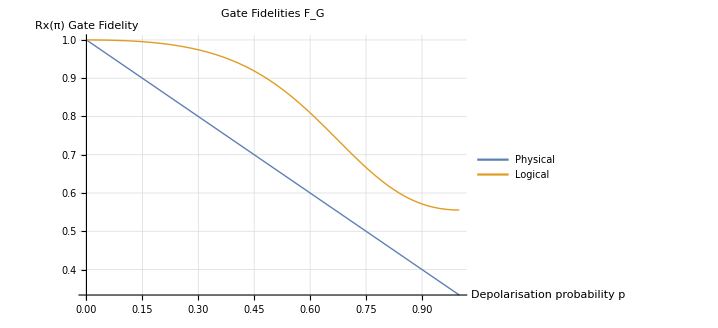

```mathematica
Plot[{CalculatePhysicalGateFidelity[p,Rx[π]],CalculateLogicalGateFidelity[p,RXπL]},{p,0,1},PlotRange->All,PlotLabel->"Gate Fidelities F_G",PlotLegends->Placed[{"Physical","Logical"},Above],AxesLabel->{Style["Depolarisation probability p",Bold,Black],Style["Rx(π) Gate Fidelity",Bold,Black]},AxesStyle->Thick,PlotStyle->Thick,GridLines->Automatic]
```

### For Rz(π)

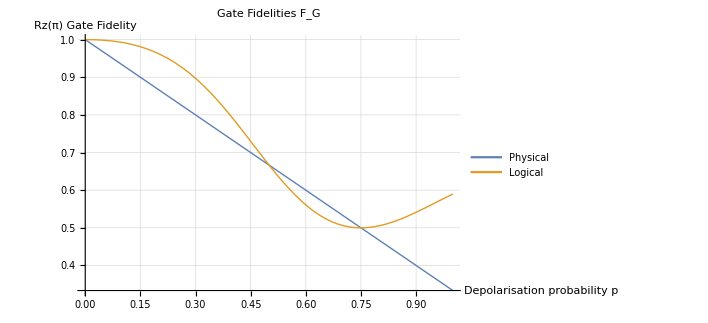

```mathematica
Plot[{CalculatePhysicalGateFidelity[p,Rz[π]],CalculateLogicalGateFidelity[p,RzπL]},{p,0,1},PlotRange->All,PlotLabel->"Gate Fidelities F_G",PlotLegends->Placed[{"Physical","Logical"},Above],AxesLabel->{Style["Depolarisation probability p",Bold,Black],Style["Rz(π) Gate Fidelity",Bold,Black]},AxesStyle->Thick,PlotStyle->Thick,GridLines->Automatic]
```